```mathematica
a=ℏ=m=1;
```

```mathematica
V[x_]:=100x;
```

```mathematica
ψ[n_,x_]:=√(2/a)Sin[(n π x)/a];
```

```mathematica
f[n_,x_]=FullSimplify[Integrate[ψ[n,x]V[x]ψ[p,x],{x,0,a}]];
```

```mathematica
fD[n_]=FullSimplify[Integrate[ψ[n,x]V[x]ψ[n,x],{x,0,a}]];
```

```mathematica
Num=10;
```

```mathematica
H=1.Table[If[p==n,(n^2 π^2)/(2m ℏ^2)+fD[n],f[n,p]],{n,1,Num},{p,1,Num}]//Chop;
```

```mathematica
E0=Last[Eigenvalues[H]]
```

39.982

```mathematica
c=Normalize[Last[Eigenvectors[H]]];
```

```mathematica
c=c/Sign[c[[1]]];
```

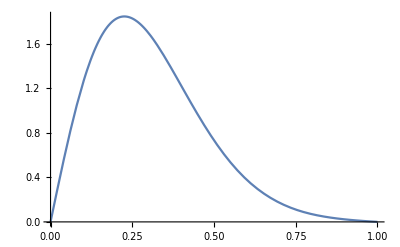

```mathematica
ψ[x_]=Sum[c[[i]]ψ[i,x],{i,1,Num}];
plot1=Plot[ψ[x],{x,0,1}]
```